```mathematica
r10=Range[0,10];
```

```mathematica
r10
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
Accumulate@r10
```

{0,1,3,6,10,15,21,28,36,45,55}

```mathematica
Subsets[r10,{2}]
```

{{0,1},{0,2},{0,3},{0,4},{0,5},{0,6},{0,7},{0,8},{0,9},{0,10},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{5,6},{5,7},{5,8},{5,9},{5,10},{6,7},{6,8},{6,9},{6,10},{7,8},{7,9},{7,10},{8,9},{8,10},{9,10}}

```mathematica
Select[Subsets[r10,{2}],Last@#-First@#==1&]
```

{{0,1},{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,10}}

```mathematica
Table[{x^2,Sin@x},{x,1,4}]
```

{{1,Sin[1]},{4,Sin[2]},{9,Sin[3]},{16,Sin[4]}}

```mathematica
MapIndexed[{#2[[1]],#1}&,Table[{x^2,Sin@x},{x,1,4}]]
```

```mathematica
Subsets[{{1,{1,Sin[1]}},{2,{4,Sin[2]}},{3,{9,Sin[3]}},{4,{16,Sin[4]}}},{2}]
```

```mathematica
Select[{{{1,{1,Sin[1]}},{2,{4,Sin[2]}}},{{1,{1,Sin[1]}},{3,{9,Sin[3]}}},{{1,{1,Sin[1]}},{4,{16,Sin[4]}}},{{2,{4,Sin[2]}},{3,{9,Sin[3]}}},{{2,{4,Sin[2]}},{4,{16,Sin[4]}}},{{3,{9,Sin[3]}},{4,{16,Sin[4]}}}},First@Last@#-First@First@#&==1]
```

{}

```mathematica
First@Last@#-First@First@#&/@{{{1,{1,Sin[1]}},{2,{4,Sin[2]}}},{{1,{1,Sin[1]}},{3,{9,Sin[3]}}},{{1,{1,Sin[1]}},{4,{16,Sin[4]}}},{{2,{4,Sin[2]}},{3,{9,Sin[3]}}},{{2,{4,Sin[2]}},{4,{16,Sin[4]}}},{{3,{9,Sin[3]}},{4,{16,Sin[4]}}}}
```

```mathematica
Subsets[r10,{2}]
```

{{0,1},{0,2},{0,3},{0,4},{0,5},{0,6},{0,7},{0,8},{0,9},{0,10},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{5,6},{5,7},{5,8},{5,9},{5,10},{6,7},{6,8},{6,9},{6,10},{7,8},{7,9},{7,10},{8,9},{8,10},{9,10}}

```mathematica
Differences
```

```mathematica
der[f_,x_,n_]:=D[f,x]/.x->n
```

```mathematica
der[Sin[x]Tan[x]+x^2,x,π]
```

2 π

```mathematica
2
```

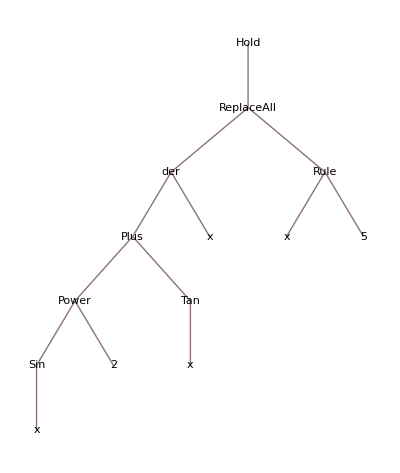

```mathematica
TreeForm@Hold[der[Sin[x]^2+Tan[x],x]/.x->5]
```

```mathematica
Outer
```

```mathematica
FoldPairList[Plus,r10]
```

FoldPair::pair: Function application 0+1 returned 1; a list of two elements is expected.

FoldPair[Plus,{0,1,2,3,4,5,6,7,8,9,10}]

```mathematica
MapThread[f[x,y],{{x1,x2,x3,...},{y1,y2,y3,...}}]
```

```mathematica
{f[x1,y1],f[x2,y2],...}
```

```mathematica
r10
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
RotateLeft[r10]
```

{1,2,3,4,5,6,7,8,9,10,0}

```mathematica
Most@MapThread[List,{r10,RotateLeft[r10]}]
```

{{0,1},{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,10}}

```mathematica
List[List[0,1],List[1,2]]
```

{{0,1},{1,2}}

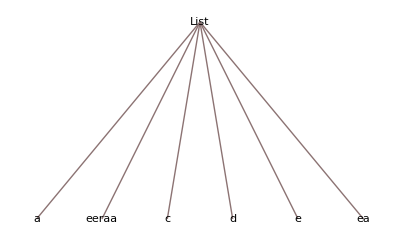

```mathematica
TreeForm@{a,eeraa,c,d,e,ea}
```

```mathematica
List[a,eeraaa,c,d,e,ea]
```

{a,eeraaa,c,d,e,ea}

```mathematica
(*Finally*)
```

```mathematica
Most@MapThread[Plus,{r10,RotateLeft[r10]}]
```

{1,3,5,7,9,11,13,15,17,19}

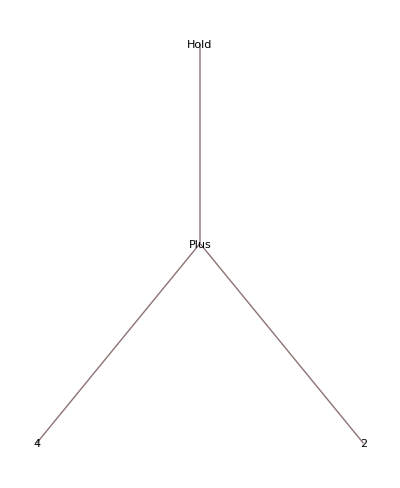

```mathematica
TreeForm@Hold[4+2]
```

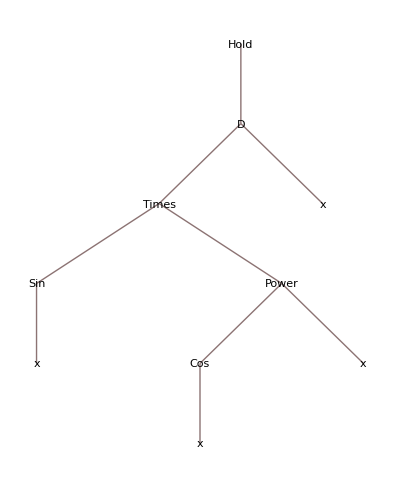

```mathematica
TreeForm@Hold@D[Sin[x] Cos[x]^x,x]
```